# 1. 平面における主な線形変換

## 1.0 図形「お」の定義

```mathematica
Oten:={{3.375,3.375},{3.625,3.625}, {4.625,2.625},{4.375,2.375},{3.375,3.375}};
Oo:={
{0.5,3.375},{0.5,3.625},{1.375,3.625},{1.375,4.5},{1.625,4.5},
{1.625,3.625},{2.5,3.625},{2.5,3.375},{1.625,3.375},{1.625,2},
{3.5,2.625},{4.625,1.5},{3.625,0.375},{3.375,0.625},{4.2,1.5},
{3.4,2.325},{1.625,1.67},{1.625,0.5},{1.375,0.5},{0.5,1.375},
{0.5,1.625},{1.375,1.925},{1.375,3.375},{0.5,3.375}
};
Onaka:={{0.9,1.45},{1.375,1.625},{1.375,1},{0.9,1.45}};
waku:={{0,0},{0,5},{5,5},{5,0},{0,0}}
```

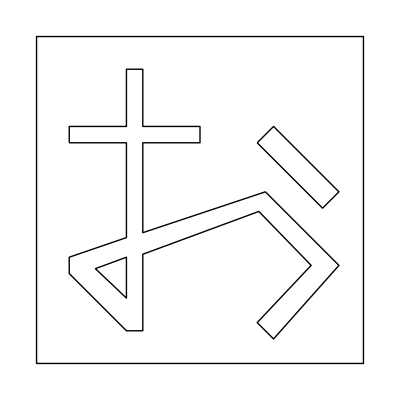

```mathematica
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}]
```

## 1.1 (1) 横方向の拡大・縮小

```mathematica
Hx[a_]:=({{a, 0}, {0, 1}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[Hx[s]]],Line[Oo.Transpose[Hx[s]]],
Line[Onaka.Transpose[Hx[s]]],Line[waku.Transpose[Hx[s]]]}
}],
Graphics[Text[Hx[s],{-8,8}]]
],{{s,1,"倍率"},-2,2},SaveDefinitions->True]
```

## 1.1 (2) 縦方向の拡大・縮小

```mathematica
Hy[a_]:=({{1, 0}, {0, a}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[Hy[s]]],Line[Oo.Transpose[Hy[s]]],
Line[Onaka.Transpose[Hy[s]]],Line[waku.Transpose[Hy[s]]]}
}],
Graphics[Text[Hy[s],{-8,8}]]
],{{s,1,"倍率"},-2,2},SaveDefinitions->True]
```

## 1.1 (3) 相似変換

```mathematica
H[a_]:=({{a, 0}, {0, a}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[H[s]]],Line[Oo.Transpose[H[s]]],
Line[Onaka.Transpose[H[s]]],Line[waku.Transpose[H[s]]]}
}],
Graphics[Text[H[s],{-8,8}]]
],{{s,1,"倍率"},-2,2},SaveDefinitions->True]
```

## 1.2 せん断

```mathematica
Shx[a_]:=({{1, a}, {0, 1}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[Shx[s]]],Line[Oo.Transpose[Shx[s]]],
Line[Onaka.Transpose[Shx[s]]],Line[waku.Transpose[Shx[s]]]}
}],
Graphics[Text[Shx[s],{-8,8}]]
],{{s,0,"横ずれの度合い"},-2,1},SaveDefinitions->True]
```

```mathematica
Shy[a_]:=({{1, 0}, {a, 1}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[Shy[s]]],Line[Oo.Transpose[Shy[s]]],
Line[Onaka.Transpose[Shy[s]]],Line[waku.Transpose[Shy[s]]]}
}],
Graphics[Text[Shy[s],{-8,8}]]
],{{s,0,"縦ずれの度合い"},-2,1},SaveDefinitions->True]
```

## 1.3 原点を中心とする回転変換

```mathematica
R[s_]:=({{Cos[s], -Sin[s]}, {Sin[s], Cos[s]}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[R[s]]],Line[Oo.Transpose[R[s]]],
Line[Onaka.Transpose[R[s]]],Line[waku.Transpose[R[s]]]}
}],
Graphics[Text[R[s],{-6,8}]]
],{s,0,2Pi},SaveDefinitions->True]
```

## 1.4 原点を通る直線に関する対称変換（鏡映）

```mathematica
S[s_]:=({{Cos[s], Sin[s]}, {Sin[s], -Cos[s]}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[S[s]]],Line[Oo.Transpose[S[s]]],
Line[Onaka.Transpose[S[s]]],Line[waku.Transpose[S[s]]]}
}],
Graphics[{Thick,Red,Line[{10*{Cos[s/2],Sin[s/2]},10*{-Cos[s/2],-Sin[s/2]}}]}],
Graphics[Text[S[s],{-6,8}]]
],{s,0,2Pi},SaveDefinitions->True]
```

## 1.5 一般のアフィン変換

```mathematica
A2[a11_,a12_,a21_,a22_]:=({{a11, a12}, {a21, a22}});
Manipulate[
Show[
Graphics[{Arrow[{{-20,0},{20,0}}],Arrow[{{0,-20},{0,20}}]},PlotRange->{{-20,20},{-20,20}}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[A2[a11,a12,a21,a22]]+{{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2}}],Line[Oo.Transpose[A2[a11,a12,a21,a22]]+{{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2}}],
Line[Onaka.Transpose[A2[a11,a12,a21,a22]]+{{v1,v2},{v1,v2},{v1,v2},{v1,v2}}],Line[waku.Transpose[A2[a11,a12,a21,a22]]+{{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2}}]}
}]
],{{a11,1,"表現行列の(1,1)成分"},-2,2},{{a12,0,"表現行列の(1,2)成分"},-2,2},{{a21,0,"表現行列の(2,1)成分"},-2,2},{{a22,1,"表現行列の(2,2)成分"},-2,2},
{{v1,0,"平行移動ベクトルの第1成分"},-5,5},{{v2,0,"平行移動ベクトルの第2成分"},-5,5},SaveDefinitions->True]
```

# 2. 空間における主な線形変換

## 2.0 立方体の面のデータ

```mathematica
P1:=5*{{0,0,0},{1,0,0},{1,1,0},{0,1,0},{0,0,0}};
P6:=5*{{0,0,1},{1,0,1},{1,1,1},{0,1,1},{0,0,1}};
P2:=5*{{0,0,0},{1,0,0},{1,0,1},{0,0,1},{0,0,0}};
P4:=5*{{0,1,0},{1,1,0},{1,1,1},{0,1,1},{0,1,0}};
P3:=5*{{0,0,0},{0,1,0},{0,1,1},{0,0,1},{0,0,0}};
P5:=5*{{1,0,0},{1,1,0},{1,1,1},{1,0,1},{1,0,0}};
```

```mathematica
Graphics3D[{Polygon[P1],Polygon[P2],Polygon[P3],Polygon[P4],Polygon[P5],Polygon[P6]}]
```

-Graphics3D-

## 2.1 相似変換

```mathematica
H3[s_]:=({{s, 0, 0}, {0, s, 0}, {0, 0, s}});
Manipulate[
Show[
Graphics3D[
{Arrow[{{-20,0,0},{20,0,0}}],Text["x軸",{21.5,0,0}],
Arrow[{{0,-20,0},{0,20,0}}],Text["y軸",{0,21.5,0}],
Arrow[{{0,0,-20},{0,0,20}}],Text["z軸",{0,0,21.5}]},Boxed->False
],
Graphics3D[{
Polygon[P1.Transpose[H3[s]]],
Polygon[P2.Transpose[H3[s]]],
Polygon[P3.Transpose[H3[s]]],
Polygon[P4.Transpose[H3[s]]],
Polygon[P5.Transpose[H3[s]]],
Polygon[P6.Transpose[H3[s]]]}],
Graphics3D[{Dashed,Line[P1],Line[P2],Line[P3],Line[P4],Line[P5],Line[P6]}],
Graphics3D[Text[H3[s],{-10,-10,20}]]
],
{{s,1,"拡大・縮小率"},-3,3},
SaveDefinitions->True]
```

## 2.3 (1) z軸を回転軸とする回転

```mathematica
Rz[s_]:=({{Cos[s], -Sin[s], 0}, {Sin[s], Cos[s], 0}, {0, 0, 1}});
Manipulate[
Show[
Graphics3D[
{Arrow[{{-10,0,0},{10,0,0}}],Text["x軸",{11.5,0,0}],
Arrow[{{0,-10,0},{0,10,0}}],Text["y軸",{0,11.5,0}],
Arrow[{{0,0,-10},{0,0,10}}],Text["z軸",{0,0,11.5}]},Boxed->False
],
Graphics3D[{
Polygon[P1.Transpose[Rz[s]]],
Polygon[P2.Transpose[Rz[s]]],
Polygon[P3.Transpose[Rz[s]]],
Polygon[P4.Transpose[Rz[s]]],
Polygon[P5.Transpose[Rz[s]]],
Polygon[P6.Transpose[Rz[s]]]}],
Graphics3D[{Dashed,Line[P1],Line[P2],Line[P3],Line[P4],Line[P5],Line[P6]}],
Graphics3D[Text[Rz[s],{-5,-5,10}]]
],
{{s,0,"回転角"},0,2Pi},
SaveDefinitions->True]
```

## 2.3 (2) x軸を回転軸とする回転

```mathematica
Rx[s_]:=({{1, 0, 0}, {0, Cos[s], -Sin[s]}, {0, Sin[s], Cos[s]}});
Manipulate[
Show[
Graphics3D[
{Arrow[{{-10,0,0},{10,0,0}}],Text["x軸",{11.5,0,0}],
Arrow[{{0,-10,0},{0,10,0}}],Text["y軸",{0,11.5,0}],
Arrow[{{0,0,-10},{0,0,10}}],Text["z軸",{0,0,11.5}]},Boxed->False
],
Graphics3D[{
Polygon[P1.Transpose[Rx[s]]],
Polygon[P2.Transpose[Rx[s]]],
Polygon[P3.Transpose[Rx[s]]],
Polygon[P4.Transpose[Rx[s]]],
Polygon[P5.Transpose[Rx[s]]],
Polygon[P6.Transpose[Rx[s]]]}],
Graphics3D[{Dashed,Line[P1],Line[P2],Line[P3],Line[P4],Line[P5],Line[P6]}],
Graphics3D[Text[Rx[s],{-5,-5,10}]]
],
{{s,0,"回転角"},0,2Pi},
SaveDefinitions->True]
```

## 2.3 (3) y軸を回転軸とする回転

```mathematica
Ry[s_]:=({{Cos[s], 0, Sin[s]}, {0, 1, 0}, {-Sin[s], 0, Cos[s]}});
Manipulate[
Show[
Graphics3D[
{Arrow[{{-10,0,0},{10,0,0}}],Text["x軸",{11.5,0,0}],
Arrow[{{0,-10,0},{0,10,0}}],Text["y軸",{0,11.5,0}],
Arrow[{{0,0,-10},{0,0,10}}],Text["z軸",{0,0,11.5}]},Boxed->False
],
Graphics3D[{
Polygon[P1.Transpose[Ry[s]]],
Polygon[P2.Transpose[Ry[s]]],
Polygon[P3.Transpose[Ry[s]]],
Polygon[P4.Transpose[Ry[s]]],
Polygon[P5.Transpose[Ry[s]]],
Polygon[P6.Transpose[Ry[s]]]}],
Graphics3D[{Dashed,Line[P1],Line[P2],Line[P3],Line[P4],Line[P5],Line[P6]}],
Graphics3D[Text[Ry[s],{-5,-5,10}]]
],
{{s,0,"回転角"},0,2Pi},
SaveDefinitions->True]
```

## 2.3 (4) 原点を通る直線を回転軸とする回転

```mathematica
ax[u_,v_]:=Cos[u]*Cos[v];
ay[u_,v_]:=Sin[u]*Cos[v];
az[u_,v_]:=Sin[v];R3[s_][u_,v_]:=({{Cos[s]+(1-Cos[s])*(ax[u,v])^2, (1-Cos[s])*ax[u,v]*ay[u,v]-az[u,v]*Sin[s], (1-Cos[s])*ax[u,v]*az[u,v]+ay[u,v]*Sin[s]}, {(1-Cos[s])*ax[u,v]*ay[u,v]+az[u,v]*Sin[s], Cos[s]+(1-Cos[s])*(ay[u,v])^2, (1-Cos[s])*ay[u,v]*az[u,v]-ax[u,v]*Sin[s]}, {(1-Cos[s])*ax[u,v]*az[u,v]-ay[u,v]*Sin[s], (1-Cos[s])*ay[u,v]*az[u,v]+ax[u,v]*Sin[s], Cos[s]+(1-Cos[s])*(az[u,v])^2}});
Manipulate[
Show[
Graphics3D[
{Arrow[{{-10,0,0},{10,0,0}}],Text["x軸",{11.5,0,0}],
Arrow[{{0,-10,0},{0,10,0}}],Text["y軸",{0,11.5,0}],
Arrow[{{0,0,-10},{0,0,10}}],Text["z軸",{0,0,11.5}]},Boxed->False
],
Graphics3D[{Thick,Red,Line[{-10*{ax[u[[1]],u[[2]]],ay[u[[1]],u[[2]]],az[u[[1]],u[[2]]]},10*{ax[u[[1]],u[[2]]],ay[u[[1]],u[[2]]],az[u[[1]],u[[2]]]}}]}],
Graphics3D[{
Polygon[P1.Transpose[R3[s][u[[1]],u[[2]]]]],
Polygon[P2.Transpose[R3[s][u[[1]],u[[2]]]]],
Polygon[P3.Transpose[R3[s][u[[1]],u[[2]]]]],
Polygon[P4.Transpose[R3[s][u[[1]],u[[2]]]]],
Polygon[P5.Transpose[R3[s][u[[1]],u[[2]]]]],
Polygon[P6.Transpose[R3[s][u[[1]],u[[2]]]]]}],
Graphics3D[{Dashed,Line[P1],Line[P2],Line[P3],Line[P4],Line[P5],Line[P6]}],
Graphics3D[Text[R3[s][u[[1]],u[[2]]],{-5,-5,10}]]
],
{{u,{Pi/2,Pi/2},"回転軸"},{0,0},{2Pi,Pi/2}},
Delimiter,{{s,0,"回転角"},0,2Pi},
SaveDefinitions->True, ControlPlacement->Left
]
```

## 2.4 原点を通る平面に関する対称変換（鏡映）

```mathematica
ax[u_,v_]:=Cos[u]*Cos[v];
ay[u_,v_]:=Sin[u]*Cos[v];
az[u_,v_]:=Sin[v];
S3[u_,v_]:=({{1-2ax[u,v]^2, -2ax[u,v]*ay[u,v], -2ax[u,v]*az[u,v]}, {-2ax[u,v]*ay[u,v], 1-2ay[u,v]^2, -2ay[u,v]*az[u,v]}, {-2ax[u,v]*az[u,v], -2ay[u,v]*az[u,v], 1-2az[u,v]^2}});
Manipulate[
Show[
Graphics3D[
{Arrow[{{-10,0,0},{10,0,0}}],Text["x軸",{11.5,0,0}],
Arrow[{{0,-10,0},{0,10,0}}],Text["y軸",{0,11.5,0}],
Arrow[{{0,0,-10},{0,0,10}}],Text["z軸",{0,0,11.5}]},Boxed->False
],
Graphics3D[{
Polygon[P1.Transpose[S3[u[[1]],u[[2]]]]],
Polygon[P2.Transpose[S3[u[[1]],u[[2]]]]],
Polygon[P3.Transpose[S3[u[[1]],u[[2]]]]],
Polygon[P4.Transpose[S3[u[[1]],u[[2]]]]],
Polygon[P5.Transpose[S3[u[[1]],u[[2]]]]],
Polygon[P6.Transpose[S3[u[[1]],u[[2]]]]]}],
Graphics3D[{Dashed,Line[P1],Line[P2],Line[P3],Line[P4],Line[P5],Line[P6]}],
ContourPlot3D[ax[u[[1]],u[[2]]]*X+ay[u[[1]],u[[2]]]*Y+az[u[[1]],u[[2]]]*Z==0,
{X,-11.5,11.5},{Y,-11.5,11.5},{Z,-11.5,11.5},Mesh->None,ContourStyle->Directive[Orange,Opacity[0.5]]
],
Graphics3D[{Blue,Thick,Arrow[{{0,0,0},8{ax[u[[1]],u[[2]]],ay[u[[1]],u[[2]]],az[u[[1]],u[[2]]]}}]}],
Graphics3D[Text[S3[u[[1]],u[[2]]],{-7,-7,10}]]
],
Delimiter,Style["平面の法線ベクトル",12,Bold],
{{u,{2Pi,Pi/2},"方向"},{0,0},{2Pi,Pi/2}},
SaveDefinitions->True, ControlPlacement->Left
]
```

## 2.5 一般の線形変換

```mathematica
M[a11_,a12_,a13_,a21_,a22_,a23_,a31_,a32_,a33_]:=({{a11, a12, a13}, {a21, a22, a23}, {a31, a32, a33}});
Manipulate[
Show[
Graphics3D[
{Arrow[{{-20,0,0},{20,0,0}}],Text["x軸",{21.5,0,0}],
Arrow[{{0,-20,0},{0,20,0}}],Text["y軸",{0,21.5,0}],
Arrow[{{0,0,-20},{0,0,20}}],Text["z軸",{0,0,21.5}]},Boxed->False
],
Graphics3D[{
Polygon[P1.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]],
Polygon[P2.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]],
Polygon[P3.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]],
Polygon[P4.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]],
Polygon[P5.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]],
Polygon[P6.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]],
Text[M[a1,a2,a3,b1,b2,b3,c1,c2,c3],{-15,-15,15}]
}],
Graphics3D[{Dashed,Line[P1],Line[P2],Line[P3],Line[P4],Line[P5],Line[P6]}]
],
Style["行列の第1列の成分",12,Bold],
{{a1,1,"第1行"},-4,4},{{b1,0,"第2行"},-4,4},{{c1,0,"第3行"},-4,4},
Delimiter,Style["行列の第1列の成分",12,Bold],
{{a2,0,"第1行"},-4,4},{{b2,1,"第2行"},-4,4},{{c2,0,"第3行"},-4,4},
Delimiter,Style["行列の第1列の成分",12,Bold],
{{a3,0,"第3行"},-4,4},{{b3,0,"第3行"},-4,4},{{c3,1,"第3行"},-4,4},
SaveDefinitions->True, ControlPlacement->Left
]
```

## 2.6 一般のアフィン変換

```mathematica
Manipulate[
Show[
Graphics3D[
{Arrow[{{-20,0,0},{20,0,0}}],Text["x軸",{21.5,0,0}],
Arrow[{{0,-20,0},{0,20,0}}],Text["y軸",{0,21.5,0}],
Arrow[{{0,0,-20},{0,0,20}}],Text["z軸",{0,0,21.5}]},Boxed->False
],
Graphics3D[{
Polygon[P1.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]+{{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3}}],
Polygon[P2.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]+{{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3}}],
Polygon[P3.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]+{{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3}}],
Polygon[P4.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]+{{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3}}],
Polygon[P5.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]+{{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3}}],
Polygon[P6.Transpose[M[a1,a2,a3,b1,b2,b3,c1,c2,c3]]+{{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3},{v1,v2,v3}}],
Text[M[a1,a2,a3,b1,b2,b3,c1,c2,c3],{-15,-15,15}]
}],
Graphics3D[{Dashed,Line[P1],Line[P2],Line[P3],Line[P4],Line[P5],Line[P6]}]
],
Style["行列の第1列の成分",12,Bold],
{{a1,1,"第1行"},-4,4},{{b1,0,"第2行"},-4,4},{{c1,0,"第3行"},-4,4},
Delimiter,Style["行列の第1列の成分",12,Bold],
{{a2,0,"第1行"},-4,4},{{b2,1,"第2行"},-4,4},{{c2,0,"第3行"},-4,4},
Delimiter,Style["行列の第1列の成分",12,Bold],
{{a3,0,"第3行"},-4,4},{{b3,0,"第3行"},-4,4},{{c3,1,"第3行"},-4,4},
Delimiter,Style["平行移動ベクトルの成分",12,Bold],
{{v1,0,"第1成分"},-5,5},{{v2,0,"第2成分"},-5,5},{{v3,0,"第3成分"},-5,5},
SaveDefinitions->True, ControlPlacement->Left
]
```